```mathematica
f[x_]:=x^2
```

```mathematica
Or[False,False]
Or[False,True]
Or[True,False]
Or[True,True]
```

False

True

True

True

```mathematica
And[False,False]
And[False,True]
And[True,False]
And[True,True]
```

False

False

False

True

```mathematica
Nor[False,False]
Nor[False,True]
Nor[True,False]
Nor[True,True]
```

True

False

False

False

#### xor用来测试是否相同，

```mathematica
Xor[False,False]
Xor[False,True]
Xor[True,False]
Xor[True,True]
```

False

True

True

False

## 关于遗传算法的讨论

Perfect Deterministic system       决定论系统
I know perfect initial conditions
I know perfectly the laws which allow me to move from t=1 to t=2 and t=n

Non deterministric   无法预测的
混沌有两种存在方式，决定性的和非决定性的




遗传算法步骤
一、产生个体（染色体，chromosome）
二、评估个体（适应度，fitness）
三、筛选配对（selection，适应度越高，选择概率越大的原则，从种群中选择两个个体作为父方和母方。）
四、交叉繁殖（
五、适当变异（mutation rate]
六、循环迭代


运行参数
是否选择精英操作
种群大小
染色体长度
最大迭代次数
交叉概率
变异概率

一般来说，交叉概率(cross_rate)比较大，变异概率(mutate_rate)极低。像求解函数最大值这类问题，我设置的交叉概率(cross_rate)是0.6，变异概率(mutate_rate)是0.01。

convergence rate通过迭代次数来评估算法的收敛速度，迭代速度越少，说明收敛速度越快

HammingDistance用来检测两个序列的差距从而用来评估

What I want to obtain: Philippe
Input: akuhdls
next: liqqkdip
next: phefios
next: phekipe
next: phrlipz
next: phelippt...

```mathematica
Graphics[Circle[]];
```

不同的序列都可以比较差距

```mathematica
{0,1,0,0,0,1,1,1,0,1,0,0,1}
{a,b,c,d,e,f,g}
```

{0,1,0,0,0,1,1,1,0,1,0,0,1}

{a,b,c,d,e,f,g}

以下是phenotype表现型

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### 所有东西都可以量化，比如字母

```mathematica
ToCharacterCode[{"z","i","d","o","n","g"}]
```

{{122},{105},{100},{111},{110},{103}}

```mathematica
ToCharacterCode[{"z","i","d","o","n","g"}]-ToCharacterCode[{"x","i","a","n","g","x"}]
```

{{2},{0},{3},{1},{7},{-17}}

```mathematica
Total[Flatten[Abs/@{{2},{0},{3},{1},{7},{-17}}]]
```

30

结果30就是所谓的汉明距离，hamming distance

#### 具体而言，我们的任务是: objective/aims/goal(what you want to obtain) 设置目标 initial list 初始数列 random mutation function 随机变异函数 crossover function(一半遗传自父方，一半来自于母方）：parent:{a,b,c,d,e,f,g,h} {h,i,j,k,l,m,n,o} child: {a,b,c,d,l,m,n,o} distance function(evaluating the similarity（评估） function produce a lot of mutated list（繁殖） function keep the best ones(based on the criteria defined by the distance function)

## 我们从二进制列表binary list开始，设置一个测试列表

首先随机产生一个列表

```mathematica
lengthOfmysequence=20
```

20

```mathematica
RandomInteger[]
```

1

```mathematica
sequenceTest=Table[RandomInteger[],{lengthOfmysequence}]
```

{0,0,0,1,1,0,1,1,1,0,1,1,0,0,0,1,0,0,1,1}

```mathematica
sequenceTest
```

{0,0,0,1,1,0,1,1,1,0,1,1,0,0,0,1,0,0,1,1}

```mathematica
Sort[sequenceTest]
```

{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1}

```mathematica
ConstantArray[0,5]
```

{0,0,0,0,0}

```mathematica
Table[0,5]
```

{0,0,0,0,0}

所以我们可以创一个随机序列

```mathematica
initialList[a_]:=Table[RandomInteger[],{a}]
```

```mathematica
initialList[5]
```

{1,1,0,1,1}

## 设置一个标准序列，用来检测数列

```mathematica
listInit=ConstantArray[0,lengthOfmysequence]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## 随机变异函数

#### 从1到20挑出序列里面一个数

```mathematica
RandomInteger[{1,lengthOfmysequence}]
```

7

#### 随机挑1个数替换

```mathematica
listInit/.RandomInteger[]->RandomInteger[{1,lengthOfmysequence}]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
listInit/.RandomInteger[]:>RandomInteger[{1,lengthOfmysequence}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ReplacePart[listInit,RandomInteger[]:>RandomInteger[{1,lengthOfmysequence}]]
```

{5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ReplacePart[listInit,RandomInteger[{1,lengthOfmysequence}]->RandomInteger[]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ReplacePart[listInit,RandomInteger[{1,lengthOfmysequence}]:>RandomInteger[]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### 随机每次替换n个数

```mathematica
Clear[mutFun1]
mutFun1[listToMut_,n_]:=
  ReplacePart[listToMut, Table[RuleDelayed[RandomInteger[{1,lengthOfmysequence}],RandomInteger[]],{i,1,n}]]
```

```mathematica
listInit
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Clear[mutFun1]
mutFun1[listToMut_,n_]:=
  ReplacePart[listToMut, Table[RandomInteger[{1,lengthOfmysequence}]->RandomInteger[],{i,1,n}]]
```

```mathematica
mutFun1[listInit,1]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0}

```mathematica
mutFun1[listInit,2]
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}

#### 如果要把每一次都表现出来

```mathematica
Table[listInit=mutFun1[listInit,2],{5}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0)

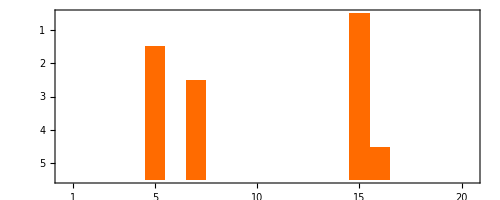

```mathematica
%//MatrixPlot
```

## 设置交叉互换函数

```mathematica
a={1,2,3,4};
b={5,6,7,8};
Take[a,Length[a]/2];
Take[b,-Length[b]/2];
```

```mathematica
Join[Take[a,Length[a]/2],Take[b,-Length[b]/2]]
```

{1,2,7,8}

```mathematica
crossFun[lista_,listb_]:=Join[Take[lista,Length[lista]/2],Take[listb,-Length[listb]/2]]
```

```mathematica
crossFun[{1,2,3,4},{5,6,7,8}]
```

{1,2,7,8}

#### 老师有一个更加复杂的交叉变化

```mathematica
listInit[[RandomInteger[{1,lengthOfmysequence}]]]=RandomInteger[]
```

1

```mathematica
teacherFun[a_/;EvenQ[Length[a]],b_]/;b<Length[a]/2:=
Module[{centerOfMutation=RandomInteger[{1,Length[a]}],
outputList=Join[a,a,a]},
Table[outputList[[i]]=RandomInteger[],
{i,centerOfMutation-b,centerOfMutation+b}];
      outputList]
```

```mathematica
teacherFun[listInit,1]
```

1[1,1,0,0,1,0,1,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,1,1,0,0,0,0]

## 评估

#### 设置检测函数和目标函数

```mathematica
sequenceTest=Table[RandomInteger[],{lengthOfmysequence}]
```

{1,1,0,1,1,1,0,1,0,0,0,1,0,1,1,0,0,1,0,0}

```mathematica
objectSequence=Join[ConstantArray[0,lengthOfmysequence/2],ConstantArray[1,lengthOfmysequence/2]]
```

{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1}

```mathematica
Riffle[Table[1,50],0]
```

{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}

#### 定义一个函数用来测量数列距离

```mathematica
Clear[funDistance]
funDistance[a_,b_]:=Total[Flatten[Abs/@{a-b}]]
```

```mathematica
funDistance[sequenceTest,objectSequence]
```

15

```mathematica
sequenceTest=Table[RandomInteger[],{lengthOfmysequence}]
```

{0,1,0,1,1,1,1,0,0,1,0,0,0,0,0,0,0,1,0,0}

#### 老师的方法，更加普遍，只要不同就可以区分出来

```mathematica
Transpose[{sequenceTest,objectSequence}]
```

{{0,0},{1,0},{0,0},{1,0},{1,0},{1,0},{1,0},{0,0},{0,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{1,1},{0,1},{0,1}}

```mathematica
Clear[funDistance]
funDistance[a_,b_]:=Count[Xor[#[[1]],#[[2]]]&/@(Transpose[{a,b}]/.{0->False,1->True}),True]
```

```mathematica
funDistance[sequenceTest,objectSequence]
```

15

## 筛选最佳

#### 生成五个sequencetest，如果单纯这样，就会出现重复。

```mathematica
sequenceTest=Table[RandomInteger[],{lengthOfmysequence}]
```

{1,0,1,0,0,0,0,1,0,1,0,1,1,1,1,0,1,1,1,0}

```mathematica
Table[funDistance[sequenceTest,objectSequence],5]
```

{7,7,7,7,7}

#### 所以要延迟输入

```mathematica
sequenceTest:=Table[RandomInteger[],{lengthOfmysequence}]
```

```mathematica
Table[funDistance[sequenceTest,objectSequence],5]
```

{13,12,10,15,8}

```mathematica
distance=Table[funDistance[sequenceTest,objectSequence],5]
```

{11,9,6,8,12}

#### 找到里面差距最小的位置

```mathematica
Position[distance,Min[distance]]
```

{{3}}

#### 得把产生的序列和他们的距离捆绑起来

```mathematica
aaa=Table[{sequenceTest,
funDistance[sequenceTest,objectSequence]},{5}]
```

{{{1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,1,0,0,1,0},8},{{0,1,1,0,0,0,0,1,1,0,0,0,1,1,1,0,0,1,0,1},12},{{1,0,1,0,1,1,1,0,0,0,1,1,0,0,1,1,1,0,1,0},9},{{1,1,1,0,1,0,1,1,1,1,1,0,1,1,0,0,1,1,0,1},11},{{0,1,0,0,0,0,1,0,1,1,0,0,1,1,0,1,1,0,0,0},7}}

#### distance可以用aaa表示，通过替换来代替从每一项选第一项！！！！以下两种方法等效！！

```mathematica
Clear[a]
aaa/.{_,a_Integer}->a
```

{11,11,11,6,10}

```mathematica
Extract[2]/@aaa
```

{11,11,11,6,10}

#### 接下来提取最好的结果

```mathematica
Extract[aaa,Position[aaa/.{_,a_Integer}->a,Min[aaa/.{_,a_Integer}->a]]]
```

{{{0,1,0,0,0,0,1,0,1,1,0,0,1,1,0,1,1,0,0,0},7}}

```mathematica
Extract[aaa,Position[Extract[2]/@aaa,Min[Extract[2]/@aaa]]]
```

{{{0,1,0,0,0,0,1,0,1,1,0,0,1,1,0,1,1,0,0,0},7}}

#### 改变形式，再一次用到替换！！

```mathematica
Extract[aaa,Position[Extract[2]/@aaa,Min[Extract[2]/@aaa]]]/.{a_,b_Integer}->a
```

{{0,1,0,0,0,0,1,0,1,1,0,0,1,1,0,1,1,0,0,0}}

#### 接下来定义函数

```mathematica
Clear[funExtractBest]
funExtractBest:=Extract[aaa,Position[Extract[2]/@aaa,Min[Extract[2]/@aaa]]]/.{a_,b_Integer}->a
```

```mathematica
(*funExtractBest:=(bbb=Module[{},(Extract[aaa,{#[[1]]}&/@Position[aaa,Min[aaa/.{_,a_Integer}->a],{2}]])/.{a_,b_Integer}->a];If[Length[bbb]>1,Flatten[Extract[bbb,RandomInteger[{1,Length[bbb]}]]],Flatten[bbb]])*)
```

## 繁殖，生成循环

#### 现在生成目标序列和实验序列

```mathematica
lengthOfmysequence=10;
initialList=Table[RandomInteger[],{lengthOfmysequence}]
objectSequence=Join[ConstantArray[0,lengthOfmysequence/2],ConstantArray[1,lengthOfmysequence/2]]
```

{1,1,0,1,1,1,0,1,0,1}

{0,0,0,0,0,1,1,1,1,1}

#### 已经有的成果

```mathematica
Clear[aaa];Clear[a]
Clear[funDistance];Clear[mutFun1];Clear[funExtractBest];

mutFun1[listToMut_,n_]:=ReplacePart[listToMut, Table[RuleDelayed[RandomInteger[{1,lengthOfmysequence}],RandomInteger[]],{i,1,n}]]
funDistance[a_,b_]:=Total[Flatten[Abs/@{a-b}]];
```

```mathematica
aaaTemp=Table[mutFun1[initialList,2],{10}]
```

{{1,1,1,1,0,1,0,1,0,1},{1,1,0,1,1,1,0,1,0,0},{1,1,0,1,1,1,0,1,0,1},{1,1,0,1,1,1,0,1,0,0},{1,1,0,0,1,1,0,1,0,1},{1,1,0,1,1,1,1,0,0,1},{1,1,0,1,1,1,0,1,0,1},{1,1,0,1,0,0,0,1,0,1},{1,1,0,1,1,1,1,1,0,1},{1,1,0,1,1,1,0,1,0,0}}

```mathematica
aaa={#,funDistance[#,objectSequence]}&/@aaaTemp
```

{{{1,1,1,1,0,1,0,1,0,1},6},{{1,1,0,1,1,1,0,1,0,0},7},{{1,1,0,1,1,1,0,1,0,1},6},{{1,1,0,1,1,1,0,1,0,0},7},{{1,1,0,0,1,1,0,1,0,1},5},{{1,1,0,1,1,1,1,0,0,1},6},{{1,1,0,1,1,1,0,1,0,1},6},{{1,1,0,1,0,0,0,1,0,1},6},{{1,1,0,1,1,1,1,1,0,1},5},{{1,1,0,1,1,1,0,1,0,0},7}}

```mathematica
funExtractBest:=Extract[aaa,Position[Extract[2]/@aaa,Min[Extract[2]/@aaa]]]/.{a_,b_Integer}->a;
ttt=funExtractBest[[1]]
```

{1,1,0,0,1,1,0,1,0,1}

## 打包

#### 逻辑是这样，设置好目标序列，随机生成一个实验序列initialList，当实验序列不等于目标序列时，从实验序列随机替换几个数，生成数个 (5) 新的序列aaaTemp，然后再从这些数列中找到最好的

```mathematica
lengthOfmysequence=30;
initialList=Table[RandomInteger[],{lengthOfmysequence}]
objectSequence=Join[ConstantArray[0,lengthOfmysequence/2],ConstantArray[1,lengthOfmysequence/2]]

Clear[aaa];
Clear[funDistance];Clear[mutFun1];Clear[funExtractBest];

mutFun1[listToMut_,n_]:=
  ReplacePart[listToMut, Table[RandomInteger[{1,lengthOfmysequence}]->RandomInteger[],{i,1,n}]]

funDistance[a_,b_]:=Total[Flatten[Abs/@{a-b}]];
finalList={};


i=0;
While[initialList=!=objectSequence,i++;
aaaTemp=Table[mutFun1[initialList,1],{10}];
aaa={#,funDistance[#,objectSequence]}&/@aaaTemp;
funExtractBest:=Extract[aaa,Position[Extract[2]/@aaa,Min[Extract[2]/@aaa]]]/.{a_,b_Integer}->a;
initialList=funExtractBest[[1]];
finalList=Append[finalList,initialList]]

Print[i;finalList]

MatrixPlot[finalList,ColorFunction->"Monochrome" ,MeshStyle->Pink,Mesh->True,ImageSize->Medium]
```

{0,0,0,1,0,0,1,0,0,0,0,1,1,1,1,1,1,1,0,0,1,0,0,1,0,1,1,0,1,1}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{{0,0,0,1,0,0,1,0,0,0,0,1,0,1,1,1,1,1,0,0,1,0,0,1,0,1,1,0,1,1},{0,0,0,1,0,0,1,0,0,0,0,1,0,1,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,1,0,0,1,0,0,0,0,0,0,1,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,0,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

-Graphics-

#### 先研究一下怎么弄循环

```mathematica
n=1;
While[n<4,Print[n];n++]
```

1

2

3

```mathematica
For[n=1,n<4,n++,Print[n]]
```

1

2

3

```mathematica
Do[Print[n],{n,4}]
```

1

2

3

4

## 关于If

```mathematica
n=1;
If[n<4,Print[n],n++]
```

1

```mathematica
Clear[f]
f[x_]:=If[EvenQ[x],x^2,If[Head[x]==Integer,x^5,If[Head[x]==Real,x=0]]];
f[3]
f[2]
f[4]
f[0.1]
```

243

4

16

If[Real==Integer,0.1^5,If[Head[0.1]==Real,0.1=0]]

```mathematica
Table[Print[n],{n,4}]
```

1

2

3

4

{Null,Null,Null,Null}

```mathematica
lengthOfmysequence=20;
sequenceTest=Table[RandomInteger[],{lengthOfmysequence}];
While[funDistance[sequenceTest,objectSequence]<1,Print[sequenceTest];
                sequenceTest
```